```mathematica
{897,6985,{3,{4,5,7,10,9},{5<->9,5<->10},{{4,5,9},{5,9,10},{5,7,10}}}}
```

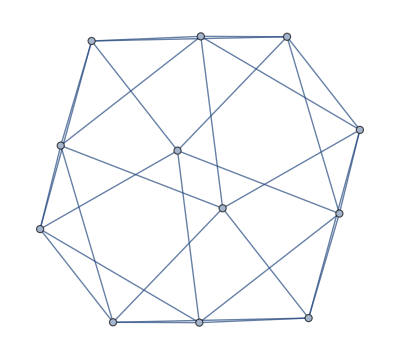

```mathematica
applied=Rule3[ReadGrof[897],{5<->9,5<->10},{4,5,7,10,9}]
```

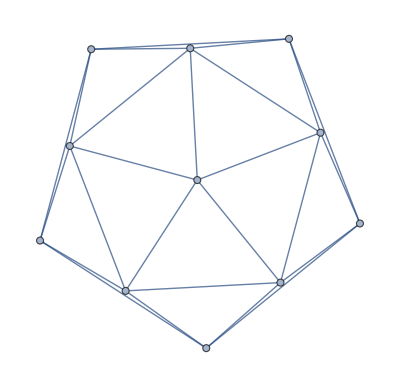

```mathematica
CenterRemoved=VertexDelete[applied,12]
```

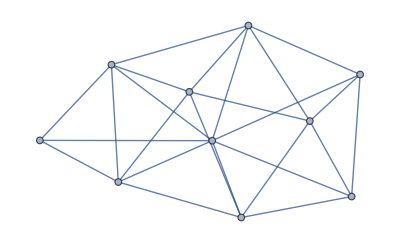

```mathematica
firstContracted=VertexContract[CenterRemoved,{5,9}]
```

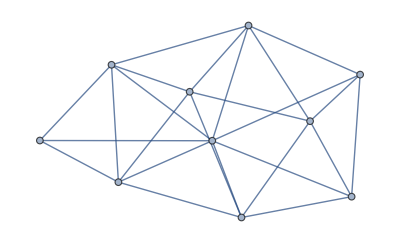

```mathematica
secondContracted=VertexContract[CenterRemoved,{4,7}]
```

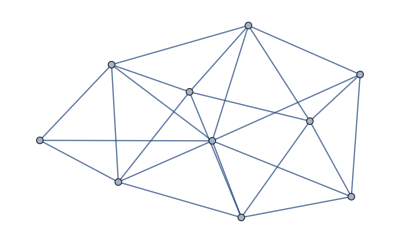

```mathematica
secondContracted2=VertexContract[CenterRemoved,{4,10}]
```

```mathematica
IsomorphicGraphQ[secondContracted,secondContracted2]
```

True

```mathematica
MaximalPlanarQ[firstContracted]
```

True

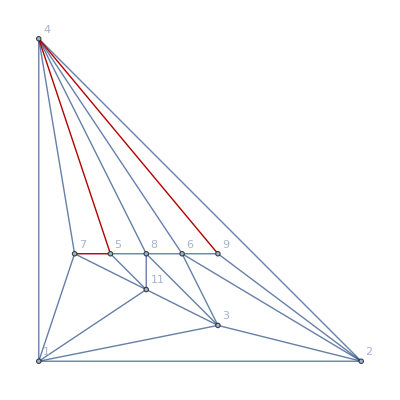

```mathematica
Graph[secondContracted2,GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlight->Rule3Cycle[{4,5,7,10,9}]]
```

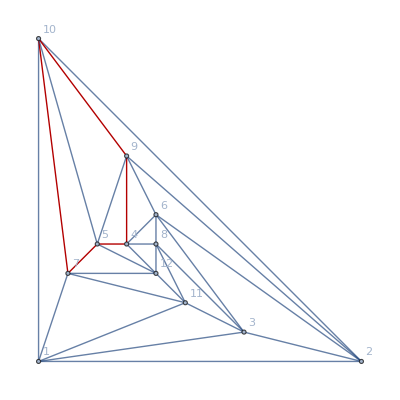

```mathematica
Graph[ReadGrof[6985],GraphLayout->"PlanarEmbedding", VertexLabels->"Name", GraphHighlight->Rule3Cycle[{4,5,7,10,9}]]
```